# Tarea 6: Interpolación de Lagrange para la funcion seno

## Generación de puntos

```mathematica
a = 1; b = 5;
datos = Table[{x,N[Sin[x]]},{x,a,b,1}]
```

{{1,0.841471},{2,0.909297},{3,0.14112},{4,-0.756802},{5,-0.958924}}

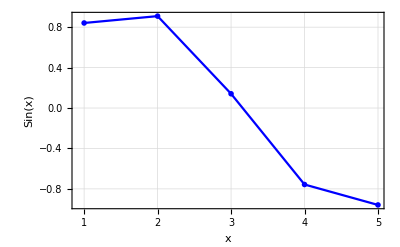

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
]
```

## Para la base de Lagrange

```mathematica
LagrangeBaseElements[xs_,i_]:=Table[If[i≠ j,(x-xs[[j+1]])/(xs[[i+1]]-xs[[j+1]]),1],{j,0,Length[xs]-1}];
LagrangeBase[xs_,i_]:=Apply[Times,LagrangeBaseElements[xs,i]];
```

```mathematica
Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

1/24 (2-x) (3-x) (4-x) (5-x)+1/6 (3-x) (4-x) (5-x) (-1+x)+1/4 (4-x) (5-x) (-2+x) (-1+x)+1/6 (5-x) (-3+x) (-2+x) (-1+x)+1/24 (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Expand@Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

1

```mathematica
LagrangeInterpolate[data_]:=Expand[data[[All,2]].Table[LagrangeBase[data[[All,1]],i],{i,0,Length[data]-1}]];
```

```mathematica
LagrangeInterpolate[datos]
```

-0.649331+2.36813 x-0.9503 x^2+0.0680069 x^3+0.00497029 x^4

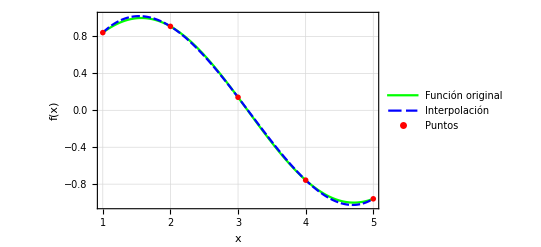

```mathematica
Show[
Plot[
{Sin[x],-0.6493310617421595+2.3681253386241785 x-0.9503004509420383 x^2+0.06800686584987492 x^3+0.004970293018039473 x^4},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue},PlotLegends->{"Función original","Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

```mathematica
"Comparacion de la interpolación por los dos métodos"
```

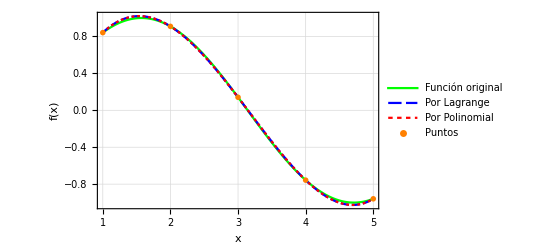

```mathematica
Show[
Plot[
{Sin[x],(-0.6493310617421595+2.3681253386241785 x-0.9503004509420383 x^2+0.06800686584987492 x^3+0.004970293018039473 x^4),(-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4)},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue,Red},PlotLegends->{"Función original","Por Lagrange","Por Polinomial"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Orange},PlotLegends->{"Puntos"}
]
]
```

```mathematica
"Comparación de la Extrapolación por los dos métodos (función mas alla de los cinco puntos)"
```

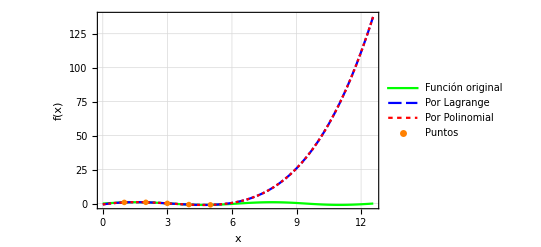

```mathematica
Show[
Plot[
{Sin[x],(-0.6493310617421595+2.3681253386241785 x-0.9503004509420383 x^2+0.06800686584987492 x^3+0.004970293018039473 x^4),(-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4)},
{x,0,4π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue,Red},PlotLegends->{"Función original","Por Lagrange","Por Polinomial"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Orange},PlotLegends->{"Puntos"}
]
]
```

```mathematica
"se puede  NOTAR que el error entre los dos metodos no difiere tanto entre ambos para este caso, tanto en la interpolación como en la extrapolación"
```